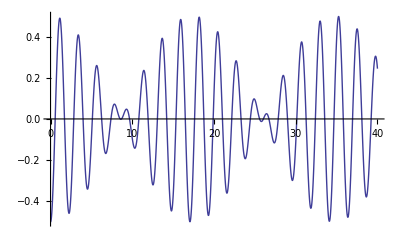

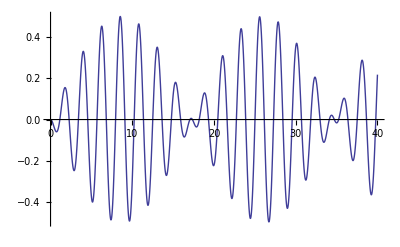

```mathematica
Clear["Global`*"]
k=1;
m1=1;
m2=1;
l=1.5;
L=2;
g=10;
T=40;

solve=NDSolve[{
m1 x1''[t]==-m1 g x1[t]/l+k (x2[t]-x1[t]),
m2 x2''[t]==-m2 g x2[t]/l-k (x2[t]-x1[t]),
x2[0]==0,
x1[0]==-.5,
x2'[0]==0,
x1'[0]==0
},{x1[t],x2[t]},{t,0,T}];

x1[t_]:=Evaluate@First[x1[t]/.solve];
x2[t_]:=Evaluate@First[x2[t]/.solve];

Plot[x1[t],{t,0,T}]
Plot[x2[t],{t,0,T}]

Animate[
Graphics[{
Line[{{-1,l},{L+1,l}}],
Line[{{0,l},{x1[t],l-Sqrt[l^2-x1[t]^2]}}],
Disk[{x1[t],l-Sqrt[l^2-x1[t]^2]},.1],
Line[{{L,l},{L+x2[t],l-Sqrt[l^2-x2[t]^2]}}],
Disk[{L+x2[t],l-Sqrt[l^2-x2[t]^2]},.1],
Dashed,Line[{{x1[t],l-Sqrt[l^2-x1[t]^2]},{L+x2[t],l-Sqrt[l^2-x2[t]^2]}}]
},
PlotRange->{{-1,L+1},{-1,l+1}}]
,{t,0,T,.1},AnimationRunning->False,AnimationRate->2]
Animate[
Graphics[{
Black,
Rectangle[{-10,-10},{10,10}],
White,
Disk[{x1[t],l-Sqrt[l^2-x1[t]^2]},.1]
},
PlotRange->{{-1,L+1},{-1,l+1}}],{t,0,T,.1},AnimationRunning->False,AnimationRate->2]
```